# 8 - answers to challenges

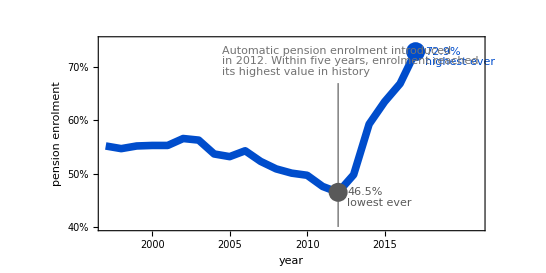

```mathematica
(* Challenge 1 *)

genLines[lines_, startPt_, spacing_, offset_, opts:OptionsPattern[Style]] := 	
	Table[Style[Text[lines⟦n+1⟧, startPt - n{0,spacing}, offset],
		  opts], {n, 0, Length[lines]-1}];

pensionProp = {55.2,54.7,55.2,55.3,55.3,56.6,56.3,53.7,53.2,54.3,52.3,50.9,50.1,49.7,47.6,46.5,49.8,59.3,63.5,66.9,72.9};
years = Range[1997,2017];
pts = Transpose[{years,pensionProp}];
low = pensionProp⟦2012-1996⟧;
high = Last[pensionProp];

hlColour = RGBColor[0,0.3,0.8];
lowColour = GrayLevel[0.35];
bgColour = GrayLevel[0.45];

subTitleText = {
	"Pension enrolment had been steadily declining since the early 2000s. As a response,",
	"the UK government introduced automatic enrolment."
};

text = {
	"Automatic pension enrolment introduced",
	"in 2012. Within five years, enrolment reached",
	"its highest value in history"
};

ListPlot[pts,
	Joined->True,
	Frame->{True,True,False,False},
	FrameLabel->{Style["year",14], Style["pension enrolment",14]},
	LabelStyle->12,
	FrameTicks->{Range[2000,2015,5],
	            {{40, "40%"}, {50,"50%"}, {60,"60%"}, {70,"70%"}}},
	PlotStyle->Directive[hlColour,Thickness[0.01]],
	PlotLabel->Style["\n",18],
	PlotRange->{{1997,2021},{40,75}},
	PlotRangeClipping->False,
	
	Epilog->{
		bgColour,
		Line[{{2012,40}, {2012,67}}],
		
		PointSize[0.025],
		lowColour, Point[{2012, low}],
		Style[Text[Row[{low,"%"}], {2012.6,low},{-1,0}],
		      FontSize->12],
		Style[Text["lowest ever", {2012.6,low-2},{-1,0}],
		      FontSize->12],
		  		      
		hlColour, Point[{2017,high}],
		Style[Text[Row[{high,"%"}], {2017.6,high},{-1,0}],
		      FontSize->12],
		Style[Text["highest ever", {2017.6,high-2},{-1,0}],
		      FontSize->12],

		bgColour,
		genLines[text, {2004.5,74}, 2, {-1,1},
			FontSize->12],
			
		Style[Text["Automatic enrolment in pensions was a huge success", {1995,79.2}, {-1,-1}],
		         FontSize->17, GrayLevel[0.3]],
		bgColour,
		genLines[subTitleText, {1995,77.5}, 1.8, {-1,-1},
			FontSize->11],
		         
		RGBColor[1,1,1,1], Thick,
		Rectangle[{2018,38}, {2021,42}]   
	},
	
	AspectRatio->1/2,
	ImageSize->Large
]
```